```mathematica
ClearAll["Global`*"]
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
(*check U*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_sm_10.csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

```mathematica
Min[Table[t[[i,2]],{i,1,Length[t]}]]
Max[Table[t[[i,2]],{i,1,Length[t]}]]
Min[Table[t[[i,3]],{i,1,Length[t]}]]
Max[Table[t[[i,3]],{i,1,Length[t]}]]
```

-0.000223587

0.000223604

-0.000447417

1.74269×10^-7

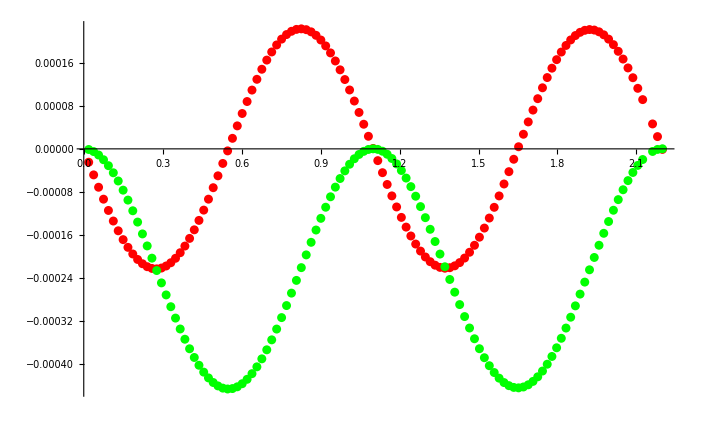

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

```mathematica
(*check nu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.0291076,1.04451},{0.0301472,1.02721},{0.0270285,1.07323},{0.0280681,1.06005},{0.0249494,1.09067},{0.025989,1.08356},{0.0228703,1.09432},{0.0239098,1.0943},{0.0207912,1.08364},{0.0218307,1.09072},{0.0187121,1.06016},{0.0197516,1.07332},{0.0166329,1.02731},{0.0176725,1.04463},{0.0145538,0.990128},{0.0155934,1.0089},{0.0124747,0.954838},{0.0135143,0.971837},{0.0103956,0.928073},{0.0114351,0.940016},{0.00831647,0.915428},{0.00935603,0.919757},{0.00623735,0.919728},{0.00727691,0.915463},{0.00415823,0.939984},{0.00519779,0.928099},{0.00207912,0.971779},{0.00311868,0.954825},{0.,1.0088},{0.00103956,0.990063}}

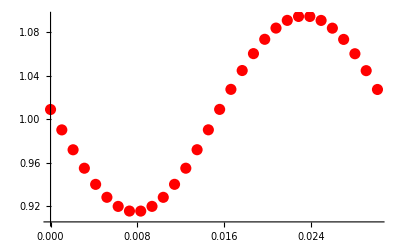

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check psi*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

{{0.0291076,4.63366},{0.0301472,4.62663},{0.0270285,4.65634},{0.0280681,4.64374},{0.0249494,4.68694},{0.025989,4.67093},{0.0228703,4.72093},{0.0239098,4.7038},{0.0207912,4.75379},{0.0218307,4.73779},{0.0187121,4.78098},{0.0197516,4.76837},{0.0166329,4.79809},{0.0176725,4.79105},{0.0145538,4.80134},{0.0155934,4.80161},{0.0124747,4.78863},{0.0135143,4.79698},{0.0103956,4.76084},{0.0114351,4.77639},{0.00831647,4.72271},{0.00935603,4.74261},{0.00623735,4.68229},{0.00727691,4.70222},{0.00415823,4.64843},{0.00519779,4.66407},{0.00207912,4.62776},{0.00311868,4.6362},{0.,4.62309},{0.00103956,4.62342}}

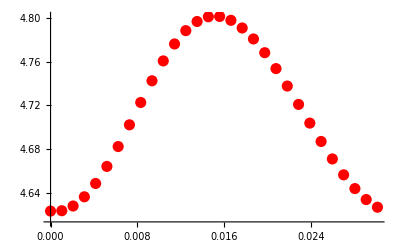

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check mu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_10.csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

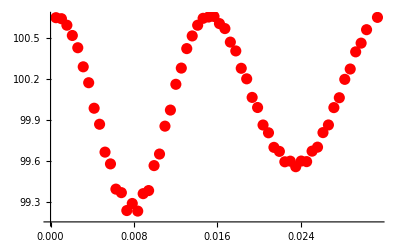

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```